DQ变换

## 1、三相静止坐标系ABC

```mathematica
U =311/1.414;
Um=Sqrt[2]*U;
a=Um*Cos[wt];
b=Um*Cos[wt-120*Pi/180];
c=Um*Cos[wt+120*Pi/180];
```

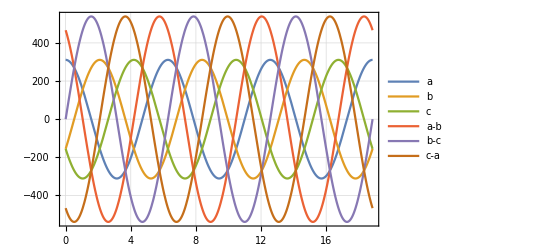

```mathematica
Plot[{a,b,c,a-b,b-c,c-a},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

三相相电压

```mathematica
ABC={{a},{b},{c}}/220;
MatrixForm[ABC]
```

(1.41385 Cos[wt]
-1.41385 Sin[π/6-wt]
-1.41385 Sin[π/6+wt])

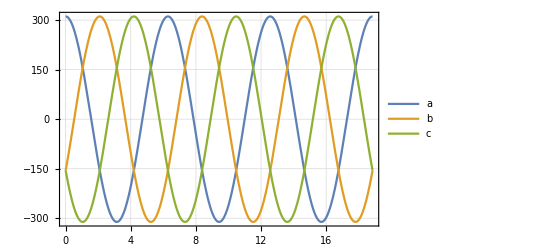

```mathematica
Plot[{a,b,c},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

三相线电压

```mathematica
LineVolt={{a-b},{b-c},{c-a}}/380;
MatrixForm[LineVolt]
```

(1/380 (311.047 Cos[wt]+311.047 Sin[π/6-wt])
1/380 (-311.047 Sin[π/6-wt]+311.047 Sin[π/6+wt])
1/380 (-311.047 Cos[wt]-311.047 Sin[π/6+wt]))

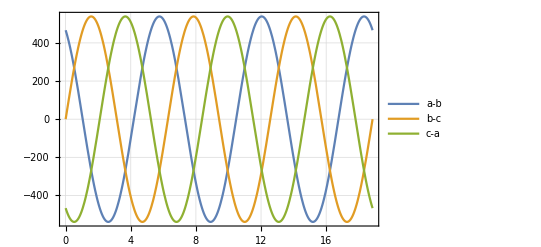

```mathematica
Plot[{a-b,b-c,c-a},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 2、三相静止坐标系ABC-两相旋转坐标系αβ

Clark变换就是三相静止坐标系ABC到两相静止坐标系αβ的变换

        Clark变换有等功率变换和等幅值变换，二者只是系数不同。以下是等功率变换：
                                  [α
β]=√(2/3)[1 | -1/2 | -1/2
0 | (√3)/2 | -(√3)/2][a
b
c]

```mathematica
ABC2AB = Sqrt[2/3]*{{1, -(1/2), -(1/2)}, {0, Sqrt[3]/2, -(Sqrt[3]/2)}}; 
MatrixForm[ABC2AB]
```

(√(2/3) | -1/(√6) | -1/(√6)
0 | 1/(√2) | -1/(√2))

通过Clark变换（等功率）从ABC坐标系变换到αβ坐标系

```mathematica
AB=ABC2AB.ABC;
MatrixForm[AB]
```

(1.1544 Cos[wt]+0.577202 Sin[π/6-wt]+0.577202 Sin[π/6+wt]
0.-0.999743 Sin[π/6-wt]+0.999743 Sin[π/6+wt])

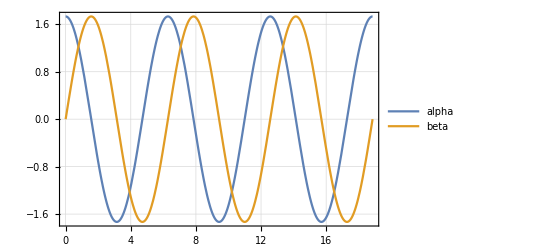

```mathematica
alpha=AB[[1,1]];
beta=AB[[2,1]];
Plot[{alpha,beta},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 3、两相静止坐标系αβ-两相旋转坐标系dq

两相静止坐标系αβ到两相旋转坐标系的变换，φ是d轴和α轴之间的夹角

        变换如下
                                     [d
q]=[cosφ | sinφ
-sinφ | cosφ][α
β]

```mathematica
AB2DQ={{Cos[wt-0*Pi/180],Sin[wt-0*Pi/180]},{-Sin[wt-0*Pi/180],Cos[wt-0*Pi/180]}};
MatrixForm[AB2DQ]
```

(Cos[wt] | Sin[wt]
-Sin[wt] | Cos[wt])

```mathematica
DQ=AB2DQ.AB;
MatrixForm[DQ]
```

(Cos[wt] (1.1544 Cos[wt]+0.577202 Sin[π/6-wt]+0.577202 Sin[π/6+wt])+Sin[wt] (0.-0.999743 Sin[π/6-wt]+0.999743 Sin[π/6+wt])
-Sin[wt] (1.1544 Cos[wt]+0.577202 Sin[π/6-wt]+0.577202 Sin[π/6+wt])+Cos[wt] (0.-0.999743 Sin[π/6-wt]+0.999743 Sin[π/6+wt]))

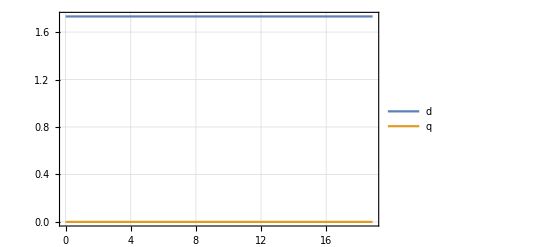

```mathematica
d=DQ[[1,1]];
q=DQ[[2,1]];
Plot[{d,q},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 4、三相静止坐标系ABC到两相旋转坐标系dq的变换

三相静止坐标系ABC到两相旋转坐标系dq的变换如下

[d
q]=√(2/3)[cosφ | -1/2cosφ+(√3)/2 sinφ | -1/2cosφ-(√3)/2 sinφ
-sinφ | 1/2 sinφ+(√3)/2 cosφ | 1/2 sinφ-(√3)/2 cosφ][a
b
c]=√(2/3)[cosφ | cos(φ-(2π)/3) | cos(φ+(2π)/3)
-sinφ | -sin(φ-(2π)/3) | -sin(φ+(2π)/3)][a
b
c]

```mathematica
CosWt = Cos[wt];
SinWt = Sin[wt];
ABC2DQZ=Sqrt[2/3]{{CosWt, -1/2 CosWt+Sqrt[3]/2 SinWt, -1/2CosWt-Sqrt[3]/2 SinWt},{-SinWt, 1/2 SinWt+Sqrt[3]/2 CosWt, 1/2 SinWt-Sqrt[3]/2 CosWt},{1/2, 1/2, 1/2}};
MatrixForm[ABC2DQZ]
```

(√(2/3) Cos[wt] | √(2/3) (-Cos[wt]/2+1/2 √3 Sin[wt]) | √(2/3) (-Cos[wt]/2-1/2 √3 Sin[wt])
-√(2/3) Sin[wt] | √(2/3) (1/2 √3 Cos[wt]+Sin[wt]/2) | √(2/3) (-1/2 √3 Cos[wt]+Sin[wt]/2)
1/(√6) | 1/(√6) | 1/(√6))

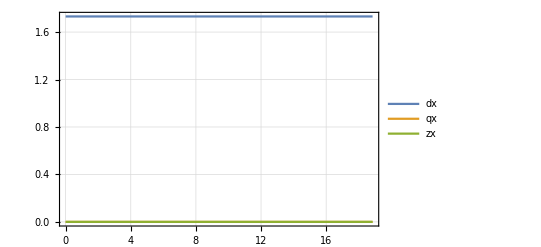

```mathematica
DQZ=ABC2DQZ.ABC;
dx=DQZ[[1,1]];
qx=DQZ[[2,1]];
zx=DQZ[[3,1]];
Plot[{dx,qx,zx},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRange->Full]
```

## 5、DQ变换的角度和实际三相电压的相角有差的影响

DQ变换的角度和实际三相电压的相角有差，例如DQ变换的角度是相电压的角度，然而三相电压是线电压

```mathematica
CosWt = Cos[wt];
SinWt = Sin[wt];
ABC2DQZ=Sqrt[2/3]{{CosWt, -1/2 CosWt+Sqrt[3]/2 SinWt, -1/2CosWt-Sqrt[3]/2 SinWt},{-SinWt, 1/2 SinWt+Sqrt[3]/2 CosWt, 1/2 SinWt-Sqrt[3]/2 CosWt},{1/2, 1/2, 1/2}};
MatrixForm[ABC2DQZ]
```

(√(2/3) Cos[wt] | √(2/3) (-Cos[wt]/2+1/2 √3 Sin[wt]) | √(2/3) (-Cos[wt]/2-1/2 √3 Sin[wt])
-√(2/3) Sin[wt] | √(2/3) (1/2 √3 Cos[wt]+Sin[wt]/2) | √(2/3) (-1/2 √3 Cos[wt]+Sin[wt]/2)
1/(√6) | 1/(√6) | 1/(√6))

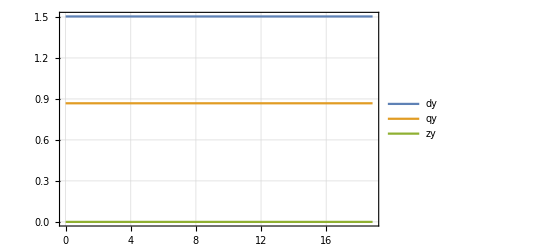

```mathematica
DQZ=ABC2DQZ.LineVolt;
dy=DQZ[[1,1]];
qy=DQZ[[2,1]];
zy=DQZ[[3,1]];
Plot[{dy,qy,zy},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRange->Full]
```

正常计算和相角有差计算得到的D轴分量之间的关系

```mathematica
beishu=TrigReduce[TrigExpand[dy/dx]]
Plot[{beishu},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRange->Full]
```

(1.50376-1.11022×10^-16 Cos[2 wt]+1.66533×10^-16 Sin[2 wt])/(1.73161+1.11022×10^-16 Cos[2 wt])

-Graphics-